# 3. izpit – Mathematica

## Računalniški praktikum 2024/25

Študijske smeri : Finančna matematika, Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## 1. naloga

1. Koliko realnih rešitev ima sistem enačb  x^2 y + y^2 x = 1  in  x^2 + y^2 = 3

2. Izračunajte vrednost izraza 1/(1·2)+1/(2·3)+1/(3·4)+…+1/(2024·2025)

3. Za katera realna števila x velja  Abs[x-2]≤3 x+7

```mathematica
Length[Solve[y*x^2 + x*y^2 ==1 && x^2 + y^2==3, {x, y}]]
Sum[1/(n*(n+1)), {n, 1, 2025}]
Reduce[Abs[x-2]<= 3x +7, x]
```

4

2025/2026

x≥-5/4

## 2. naloga

1. Definirajte funkciji f(x)=x^2+x in g(x)=(2-x)/(x^2-6x+9) ter na eni sliki narišite njuna grafa na intervalu [-2,2].

2. Grafa funkcij f in g se sekata v dveh točkah. Numerično izračunajte x in y koordinate obeh presečišč.

3. Še enkrat narišite grafa funkcij f in g ter na sliki z malima krogcema označite obe presečišči.

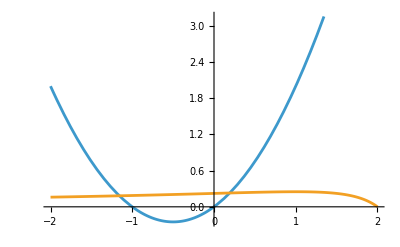

-1.15777

0.192324

0.182667

0.229312

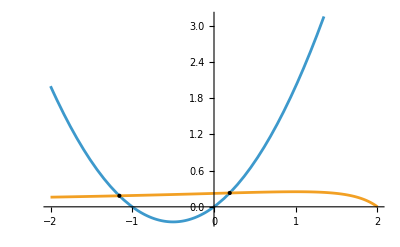

```mathematica
ClearAll[x,y,n]
f[x_]:= x^2 + x
g[x_]:=(2-x)/(x^2-6x+9)
Plot[{f[x], g[x]}, {x, -2, 2}]
x1 = x /. N[Solve[f[x]==g[x], x, Reals]][[1]]
x2 = x /. N[Solve[f[x]==g[x], x, Reals]][[2]]
y1 =N[f[x1]]
y2 = N[f[x2]]
Plot[{f[x], g[x]}, {x, -2, 2}, Epilog->{PointSize[Large],Point[{{x1, y1}, {x2, y2}}]}]
```